```mathematica
ClearAll;
```

```mathematica
(*Funciones difusas*)

WLKB1[t_] := (AKT AMPATPratio[t]);
WAMPK[t_] := (LKB1[t](1-MTORC1[t])) + (CA AMPATPratio[t](1-MTORC1[t]))+ (AKT AMPATPratio[t](1-MTORC1[t])) +(FOXP3) - (LKB1[t](1-MTORC1[t]))(CA AMPATPratio[t](1-MTORC1[t])) (AKT AMPATPratio[t](1-MTORC1[t])) (FOXP3);
WGlycolysis[t_] := MTORC1[t] (1-AMPATPratio[t]);
WOXPHOS[t_] := AMPK[t];
WAMPATPratio[t_] := Glycolysis[t](1-OXPHOS[t]);
WMTORC1[t_]:=MTOR (1-AMPK[t]);
WMTORC2[t_]:=(MTOR AMPK[t])  ;
```

```mathematica
(*Codniciones iniciales*)

LKB10= 0.; AMPK0=1.; Glycolysis0=0.; OXPHOS0=0.2; AMPATPratio0=1.; MTORC10=0.; MTORC20=0.;
```

```mathematica
(*Tasas de decaimiento*)

DLKB1= 1.; DAMPK=1.; DGlycolysis=1.; DOXPHOS=1.; DAMPATPratio = 1.; DMTORC1=1.; DMTORC2=1.;
```

```mathematica
(*Inputs*)

b=10;  MTOR=1; AKT =1; CA=1; FOXP3 =0;
```

```mathematica
(*ODEs*)

CORE2:= NDSolve[{ MTORC1'[t]==1/(1+Exp[-b(WMTORC1[t]-.5)])-DMTORC1 MTORC1[t],MTORC2'[t]==1/(1+Exp[-b(WMTORC2[t]-.5)])-DMTORC2 MTORC2[t],LKB1'[t]==1/(1+Exp[-b(WLKB1[t]-.5)])-DLKB1 LKB1[t],AMPK'[t]==1/(1+Exp[-b(WAMPK[t]-.5)])-DAMPK AMPK[t],Glycolysis'[t]==1/(1+Exp[-b(WGlycolysis[t]-.5)])-DGlycolysis Glycolysis[t],OXPHOS'[t]==1/(1+Exp[-b(WOXPHOS[t]-.5)])-DOXPHOS OXPHOS[t],AMPATPratio'[t]==1/(1+Exp[-b(WAMPATPratio[t]-.5)])-DAMPATPratio AMPATPratio[t],
MTORC1[0]==MTORC10,MTORC2[0]==MTORC20, LKB1[0]==LKB10, AMPK[0]==AMPK0, Glycolysis[0]==Glycolysis0, OXPHOS[0]==OXPHOS0, AMPATPratio[0]==AMPATPratio0 },{MTORC1[t],MTORC2[t], LKB1[t], AMPK[t], Glycolysis[t], OXPHOS[t], AMPATPratio[t]},{t,0,100}];
```

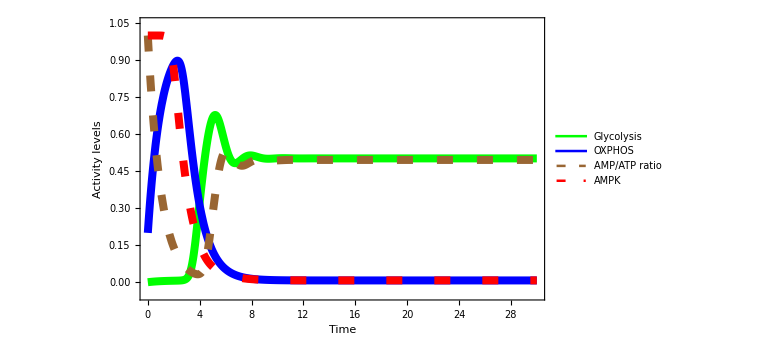

```mathematica
(*Ploteo*)

P1=Plot[Evaluate[{Glycolysis[t],OXPHOS[t], AMPATPratio[t], AMPK[t]} /. CORE2],{t,0,30},
PlotLegends->Placed[{  "Glycolysis","OXPHOS" ,"AMP/ATP ratio" , "AMPK" }, Above],
PlotRange-> {-0.05,1.05},FrameLabel->{{"Activity levels",},{"Time",""}},
PlotStyle->{{Thickness[0.01],Green},{Thickness[0.01],Blue} , {Dashing[{.02,.03}],Thickness[0.01], Darker,Brown}, {Dashing[{.02,.04}], Thickness[0.01], Darker,Red} },Frame->True,LabelStyle->Directive[Bold, Black, FontSize-> 30], ImageSize->Large]
```